# Cue-driven microbial cooperation and communication: Evolving quorum sensing with honest signalling

By: Czárán, Tamás and Scheuring, István and Zachar, István and Számadó, Szabolcs
Published in BMC Biology 2024

Supplementary material

Last modified: 2024 2. 14.
Code written by: 
	István Zachar
	istvan.zachar80@gmail.com 
	HUN-REN Institute of Evolution, Centre for Ecological Research

## Model details

N (n): random interacting group size (neighborhood size, including the focal individual);

k_c (k): cooperation threshold (critical concentration);

c_0 (c0): baseline metabolic cost (c0);

c: cost of signal detection (of cooperation);

r: signal-detection (response) cost;

b: benefit of cooperation; Only valid between 0 and 1.

d: dispersion rate (only used in the lattice model);

Coordinates are ALWAYS in the form: {x,y,z} = {Lazy, Trusty, Smart}, where z = (1-x-y).

Total concentration is rescaled to (0,1).

X (a): sum of Tr and Sm: X==y+(1-x-y)

x_k (k): the cooperation threshold concentration

## Simplex manipulation

“simplex” = 2D Cartesian coordinates on an equilateral triangle defined by coord.

"ternary" = 3D simplex coordinates on an equilateral triangle, where coordinates total to 1.

"Cartesian" = 2D Cartesian coordinates on a lower orthogonal triangle.

```mathematica
ClearAll[cartesianToSimplex,ternaryToSimplex,ternaryToCartesian,cartesianToTernary,simplexToTernary];
ClearAll[randomTernaryPoint,randomSimplexPoint,randomCartesianPoint];
ClearAll[cartesianGrid,simplexGrid,ternaryGrid];
ClearAll[graphicsToSimplex];

coord={{1,0},{1/2,Sqrt@3/2},{0,0}};
coordCartesian={{1,0},{0,1},{0,0}};
$SimplexPlotRange=MinMax/@Transpose@coord;
{xmax,ymax}=Max/@$SimplexPlotRange;
$SimplexCenter={1/2,Sqrt@3/4};
$SimplexAspectRatio=ymax/xmax;(* aspect ratio *)


$SimplexLabels={"Lazy","Trusty","Smart"};
$SimplexCornerLabels=MapThread[Text[#1,#2,#3,BaseStyle->Directive[Black,14]]&,{$SimplexLabels,coord,{{0,1},{0,-1},{0,1}}*1.5}];
$SimplexCornersCartesian=MapThread[{AbsolutePointSize@1,Point@#2,Text[#1,#2,#3,BaseStyle->Directive[Black,14]]}&,{$SimplexLabels,coordCartesian,{{0,1},{0,-1},{0,1}}*1.5}];
$SimplexBoundary={AbsoluteThickness@2,AbsolutePointSize@2,Line@PadRight[coord,{4,2},coord],Point@coord};

$SimplexPolygon=Polygon@coord;
$SimplexRegion=RegionConvert[$SimplexPolygon,"Implicit"];
$SimplexCartesianRegion=MeshRegion[{{0,0},{1,0},{0,1}},Polygon[{1,2,3}]];
$SimplexRegionFunction=Function[{x,y},(√3 x)/2+y/2≤(√3)/2&&-(√3 x)/2+y/2≤0&&-y≤0];

(* converts orthogonal lower triangular Cartesian 2D from to equilateral triangular Cartesian 2D *)
cartesianToSimplex[{x_?AtomQ,y_?AtomQ}]:={x,y,0}.coord;
cartesianToSimplex[c_List]:=cartesianToSimplex/@c;
(* converts 3D simplex coordinates to equilateral triangular Cartesian 2D *)
ternaryToSimplex[{p_?AtomQ,q_?AtomQ,r_?AtomQ}]:=coordᵀ.Normalize[{p,q,r},Total];
ternaryToSimplex[c_List]:=ternaryToSimplex/@c;
(* converts 3D simplex coordinates to orthogonal lower triangular Cartesian 2D *)
ternaryToCartesian[{p_?AtomQ,q_?AtomQ,r_?AtomQ}]:={p,q};
ternaryToCartesian[c_List]:=ternaryToCartesian/@c;
(* converts orthogonal lower triangular Cartesian 2D to 3D simplex coodinates *)
cartesianToTernary[{p_?AtomQ,q_?AtomQ}]:={p,q,1-p-q};
cartesianToTernary[c_List]:=cartesianToTernary/@c;
(* converts equilateral triangular Cartesian 2D coordinates to 3D simplex coordinates *)
simplexToTernary[{x_?AtomQ,y_?AtomQ}]:={1,0,0}+x {-1,1,0}+y {-1/Sqrt@3,-1/Sqrt@3,2/Sqrt@3};
simplexToTernary[c_List]:=simplexToTernary/@c;

randomTernaryPoint[n_Integer]:=Normalize[#,Total]&/@RandomReal[ExponentialDistribution@2,{n,3}];
randomSimplexPoint[n_Integer]:=ternaryToSimplex/@randomTernaryPoint@n;
randomCartesianPoint[n_Integer]:=ternaryToCartesian/@randomTernaryPoint@n;

cartesianGrid[d_]:=Flatten[Table[{i,j},{i,0,1,d},{j,0,1-i,d}],1];
simplexGrid[d_]:=cartesianToSimplex/@cartesianGrid@d;
ternaryGrid[d_]:=cartesianToTernary/@cartesianGrid@d;

graphicsToSimplex[g_]:=g/.{
Arrow[c_List]:>Arrow[cartesianToSimplex@c],
Text[y_,c_List,x___]:>Text[y,cartesianToSimplex@c,x],
Point[c_List]:>Point[cartesianToSimplex@c],
Disk[c_List,x___]:>Disk[cartesianToSimplex@c,x]
}/.{GraphicsComplex[c_List,x___]:>GraphicsComplex[cartesianToSimplex/@c,x]};


ClearAll[ternaryGridCoordinate];
ternaryGridCoordinate::usage="ternaryGridCoordinate[d, σ] generates a list of equidistant ternary points with distance d, wiggling the point around the expected value with a Gaussian with SD = σ.";
ternaryGridCoordinate[d:(_?NumberQ):1/10,σ_:0]:=Flatten[Table[Block[{x,y},
If[σ<=0,{x,y}={i,j},
x=Clip[RandomVariate@NormalDistribution[i,σ],{0,1}];
y=Clip[RandomVariate@NormalDistribution[j,σ],{0,1-x}];
];
{x,y,1-x-y}],{i,0,1,d},{j,0,1-i,d}],1];
```

## Mean-field model (analytic)

### Definitions

Since the cooperator density (y + z)=y+(1-x-y) is between (0,1), therefore k must be rescaled so that the domain of the sigmoid function σ is also scaled between (0,1) too.

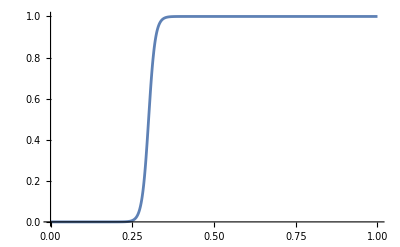

```mathematica
ClearAll[w0,r,k,c,c0,b,n,mfθ,mfσ,mfwLa,mfwTr,mfwSm,mfw,dLa,dTr,dSm,x,y];

mfθ[coop_]:=If[coop≥k,1,0];
mfσ[coop_]:=LogisticSigmoid[(coop-k)*100]; (* NOTE: If Solve chokes on the continuous sigmoid function when calculating fixed points, use mfθ instead. *)

(* Lazy, Trusty, Smart *)
mfwLa[x_,y_]:=w0-c0(1-b*mfσ[y+(1-x-y)]);
mfwTr[x_,y_]:=w0-(c0+c)*(1-b*mfσ[y+(1-x-y)+1/n]);
mfwSm[x_,y_]:=w0-(c0+r+c)*(1-b)*(mfσ[y+(1-x-y)+1/n])-(c0+r)*(1-mfσ[y+(1-x-y)+1/n]);

(* Mean fitness *)
mfw[x_,y_]:=x*mfwLa[x,y]+y*mfwTr[x,y]+(1-x-y)*mfwSm[x,y];

(* Growth equations *)
dLa[x_,y_]:=(mfwLa[x,y]-mfw[x,y])*x;
dTr[x_,y_]:=(mfwTr[x,y]-mfw[x,y])*y;
dSm[x_,y_]:=(mfwSm[x,y]-mfw[x,y])*(1-x-y);

(* NOTE: Parameter n is the interction size, not population size, hence it is set to small. *)
$MFParameterSets={
(*<|"Name"->"MF A",n->9,k->3/10,c->3/10,r->1/100,b->3/10,c0->1,w0->0|>,*)
<|"Name"->"MF A",n->9,k->3/10,c->3/10,r->1/100,b->1/10,c0->1,w0->0|>,(* NOTE: This is not the same as the usual "A", as we wanted to show a case where La does not win. *)
<|"Name"->"MF B",n->9,k->3/10,c->3/10,r->1/100,b->1/2,c0->1,w0->0|>,
<|"Name"->"MF C",n->9,k->3/10,c->3/10,r->2/10,b->65/100,c0->1,w0->0|>,
<|"Name"->"MF D",n->9,k->3/10,c->3/10,r->1/100,b->6/10,c0->1,w0->0|>
};

Plot[mfσ@c/.$MFParameterSets[[1]],{c,0,1}]
```

### Fixed point calculation

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.691527,tr→0.308473},{la→0.812652,tr→0.187348},{la→0.691999,tr→0.},{la→0.84652,tr→0.}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.690015,tr→0.},{la→0.819761,tr→0.},{la→0.683532,tr→0.316468},{la→0.817081,tr→0.182919}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.686137,tr→0.313863},{la→0.815811,tr→0.184189},{la→0.686549,tr→0.},{la→0.849739,tr→0.}}

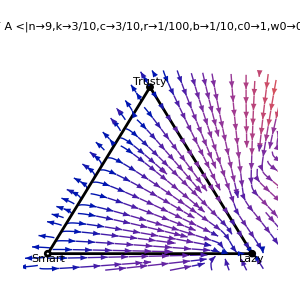
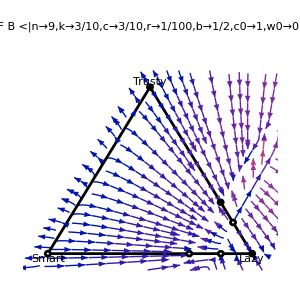
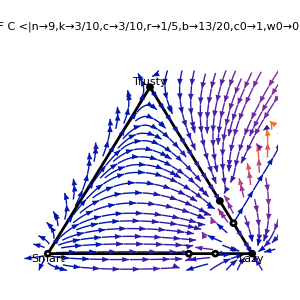
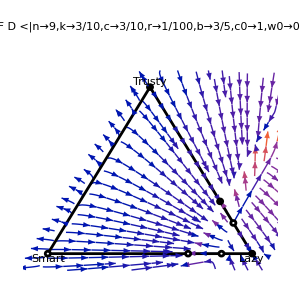

```mathematica
Block[{par=#,fp,fx,fy,x,y,Δ=.1,plot,name=#@"Name",la,tr,jacobi,eval},
fp=N@Solve[{dLa[la,tr]==0,dTr[la,tr]==0,dSm[la,tr]==0,0<=la<=1,0<=tr<=1}/.par,{la,tr},Reals];
Echo@fp;
jacobi=D[{dLa[la,tr],dTr[la,tr]},{{la,tr}}]/.fp/.par;
eval=First@MaximalBy[Eigenvalues@#,Re@*N]&/@jacobi;(* NOTE: Get dominant eigenvalues *)
fp=Thread[Chop@({la,tr,1-la-tr}/.fp)->Thread@(Re@eval<0)];
fp={EdgeForm@{AbsoluteThickness@2,Black},{FaceForm@If[Last@#,Black,White],Disk[ternaryToSimplex@First@#,Scaled@.01]}&/@fp};

{fx,fy}=Simplify/@{dLa[x,y],dTr[x,y]}/.par//N;
plot=StreamPlot[Evaluate@{fx,fy},{x,0-Δ,1+Δ},{y,0-Δ,1+Δ},
Frame->False,LabelStyle->Black,
PlotLabel->Column[{name,KeyDrop[#,"Name"]},Alignment->Center],
Epilog->{$SimplexBoundary,fp,$SimplexCornerLabels},
ImageSize->300,PlotRange->All,PlotRangePadding->{Scaled@0.05,Scaled@0.05},
Background->White,
StreamPoints->150]/.{Arrow[c_List]:>Arrow[cartesianToSimplex/@c]}/.{GraphicsComplex[c_List,x___]:>GraphicsComplex[cartesianToSimplex/@c,x]};
plot
]&/@$MFParameterSets
```

### Fixed point calculation, with hi quality vector-field BG

```mathematica
ClearAll[x,y];

$labelled=False;
$imageSize=500;
$flowPoints=500;(* Number of distinct flow lines *)
$streamColorFunction=(Directive[Opacity@.2,ColorData["SolarColors"][#3]]&);

Block[{par=#,dx,dy,x,y,fp,plot,name=#@"Name",la,tr,jacobi,eval,gridPts=randomCartesianPoint@$flowPoints},
fp=N@Solve[{dLa[la,tr]==0,dTr[la,tr]==0,dSm[la,tr]==0,0<=la<=1,0<=tr<=1}/.par,{la,tr},Reals];
Echo@fp;
jacobi=D[{dLa[la,tr],dTr[la,tr]},{{la,tr}}]/.fp/.par;
eval=First@MaximalBy[Eigenvalues@#,Re@*N]&/@jacobi;(* NOTE: Get dominant eigenvalues *)
fp=Thread[Chop@({la,tr,1-la-tr}/.fp)->Thread@(Re@eval<0)];
fp={EdgeForm@{AbsoluteThickness@2,Black},{FaceForm@If[Last@#,Black,White],Disk[ternaryToSimplex@First@#,Scaled@.01]}&/@fp};

{dx,dy}=Simplify/@{dLa[x,y],dTr[x,y]}/.par//N;
plot=Show[
StreamPlot[Evaluate@{dx,dy},{x,y}∈$SimplexCartesianRegion,
Frame->False,Mesh->False,FrameTicks->False,Ticks->False,LabelStyle->Black,
PlotLabel->If[$labelled,Column[{name,KeyDrop[par,"Name"]},Alignment->Center],None],
Epilog->{fp,{Black,If[$labelled,$SimplexCornerLabels,{}]}},
ImageSize->$imageSize,PlotRange->All,PlotRangePadding->{Scaled@0.05,Scaled@0.05},
RegionFillingStyle->None,
PerformanceGoal->"Quality",Background->White,
StreamColorFunction->$streamColorFunction,StreamColorFunctionScaling->True,StreamStyle->None,StreamPoints->{gridPts,Automatic,20}(*Fine*),StreamMarkers->"Line",StreamScale->.1
],
StreamPlot[Evaluate@{dx,dy},{x,y}∈$SimplexCartesianRegion,
RegionFillingStyle->None,
BoundaryStyle->Directive[AbsoluteThickness@2,GrayLevel@.3],PerformanceGoal->"Quality",
StreamScale->.07,StreamColorFunction->(GrayLevel[.37]&),StreamPoints->{300,.01}
]
]/.{Arrow[c_List]:>Arrow[cartesianToSimplex/@c]}/.{GraphicsComplex[c_List,x___]:>GraphicsComplex[cartesianToSimplex/@c,x]};
plot]&/@$MFParameterSets
```

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.691527,tr→0.308473},{la→0.812652,tr→0.187348},{la→0.691999,tr→0.},{la→0.84652,tr→0.}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.690015,tr→0.},{la→0.819761,tr→0.},{la→0.683532,tr→0.316468},{la→0.817081,tr→0.182919}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.686137,tr→0.313863},{la→0.815811,tr→0.184189},{la→0.686549,tr→0.},{la→0.849739,tr→0.}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Configuration-field model (analytic)

### Definitions

```mathematica
ClearAll[θ,θ1,w,wLa,wTr,wSm,fLa,fTr,fSm,gLa,gC];
ClearAll[n,k,c,r,b,d,c0,w0];

(* NOTE: x = Lazy; y = Trusty; n-1-x-y = z = Smart *)

(* Threshold functions *)
θ[x_,y_]:=If[n-1-x≥k,1,0];
θ1[x_,y_]:=If[n-1-x≥k-1,1,0];

(* Lazy and Cooperator configurations *)
gLa[x_,y_]:=Sum[Multinomial[i,j,n-1-i-j]*θ[i,j]*(x^i)*(y^j)*((1-x-y)^(n-1-i-j)),{i,0,n-1},{j,0,n-1-i}];
gC[x_,y_]:=Sum[Multinomial[i,j,n-1-i-j]*θ1[i,j]*(x^i)*(y^j)*((1-x-y)^(n-1-i-j)),{i,0,n-1},{j,0,n-1-i}];

wLa[x_,y_]:=w0-c0*(1-b*gLa[x,y]);(* Lazy fitness *)
wTr[x_,y_]:=w0-(c0+c)*(1-b*gC[x,y]);(* Trusty fitness *)
wSm[x_,y_]:=w0-(c0+r+c)*(1-b)*gC[x,y]-(c0+r)(1-gC[x,y]);(* Smart (conditional) fitness *)

(* Mean fitness *)
w[x_,y_]:=x*wLa[x,y]+y*wTr[x,y]+(1-x-y)*wSm[x,y];

(* Growth equations *)
fLa[x_,y_]:=(wLa[x,y]-w[x,y])*x;
fTr[x_,y_]:=(wTr[x,y]-w[x,y])*y;
fSm[x_,y_]:=(wSm[x,y]-w[x,y])*(1-x-y);

$ParameterSets={
<|"Name"->"CF A",n->9,k->3,c->3/10,r->1/100,b->3/10,d->0,c0->1,w0->0|>,
<|"Name"->"CF B",n->9,k->3,c->3/10,r->1/100,b->1/2,d->0,c0->1,w0->0|>,
<|"Name"->"CF C",n->9,k->3,c->3/10,r->2/10,b->65/100,d->0,c0->1,w0->0|>,
<|"Name"->"CF D",n->9,k->3,c->3/10,r->1/100,b->6/10,d->0,c0->1,w0->0|>
};
```

### Fixed point calculation

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.651696,tr→0.},{la→0.964016,tr→0.}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.671538,tr→0.},{la→0.805622,tr→0.},{la→0.579498,tr→0.420502},{la→0.7874,tr→0.2126}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.634717,tr→0.365283},{la→0.751757,tr→0.248243},{la→0.581727,tr→0.},{la→0.970079,tr→0.}}

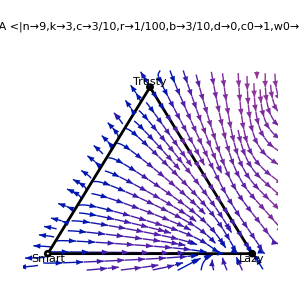
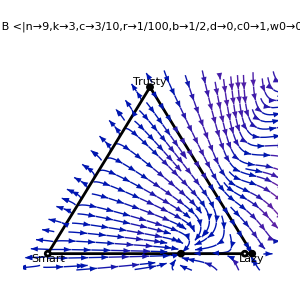
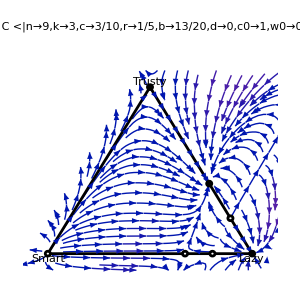
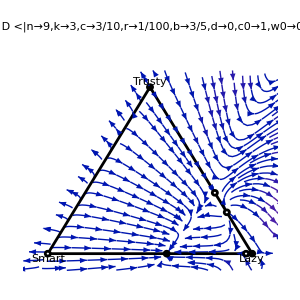

```mathematica
Block[{par=#,n=#@n,k=#@k,fp,fx,fy,x,y,Δ=.1,plot,name=#@"Name",la,tr,jacobi,eval},
fp=N@Solve[{fLa[la,tr]==0,fTr[la,tr]==0,fSm[la,tr]==0,0<=la<=1,0<=tr<=1}/.par,{la,tr}];
Echo@fp;
jacobi=D[{fLa[la,tr],fTr[la,tr]},{{la,tr}}]/.fp/.par;
eval=First@MaximalBy[Eigenvalues@#,Re@*N]&/@jacobi;(* NOTE: Get dominant eigenvalues *)
fp=Thread[Chop@({la,tr,1-la-tr}/.fp)->Thread@(Re@eval<0)];
fp={EdgeForm@{AbsoluteThickness@2,Black},{FaceForm@If[Last@#,Black,White],Disk[ternaryToSimplex@First@#,Scaled@.01]}&/@fp};
(*Echo@fp;*)

{fx,fy}=Simplify/@{fLa[x,y],fTr[x,y]}/.par//N;
plot=StreamPlot[Evaluate@{fx,fy},{x,0-Δ,1+Δ},{y,0-Δ,1+Δ},
Frame->False,LabelStyle->Black,
PlotLabel->Column[{name,KeyDrop[#,"Name"]},Alignment->Center],
Epilog->{$SimplexBoundary,fp,$SimplexCornerLabels},
ImageSize->300,PlotRange->All,PlotRangePadding->{Scaled@0.05,Scaled@0.05},
Background->White,
StreamPoints->150]/.{Arrow[c_List]:>Arrow[cartesianToSimplex/@c]}/.{GraphicsComplex[c_List,x___]:>GraphicsComplex[cartesianToSimplex/@c,x]};
plot
]&/@$ParameterSets
```

### Fixed point calculation, with hi quality vector-field BG

```mathematica
ClearAll[x,y];

$labelled=False;
$imageSize=500;
$flowPoints=500;(* Number of distinct flow lines *)
$streamColorFunction=(Directive[Opacity@.2,ColorData["BlueGreenYellow"][#3]]&);

Table[Block[{fx,fy,fp,plot,name=par@"Name",n=par@n,k=par@k,la,tr,jacobi,eval,gridPts=randomCartesianPoint@$flowPoints},

fp=N@Solve[{fLa[la,tr]==0,fTr[la,tr]==0,fSm[la,tr]==0,0<=la<=1,0<=tr<=1}/.par,{la,tr}];
Echo@fp;
jacobi=D[{fLa[la,tr],fTr[la,tr]},{{la,tr}}]/.fp/.par;
eval=First@MaximalBy[Eigenvalues@#,Re@*N]&/@jacobi;(* NOTE: Get dominant eigenvalues *)
fp=Thread[Chop@({la,tr,1-la-tr}/.fp)->Thread@(Re@eval<0)];
fp={EdgeForm@{AbsoluteThickness@2,Black},{FaceForm@If[Last@#,Black,White],Disk[ternaryToSimplex@First@#,Scaled@.01]}&/@fp};

{fx,fy}=Simplify/@{fLa[x,y],fTr[x,y]}/.par//N;
plot=Show[
StreamPlot[Evaluate@{fx,fy},{x,y}∈$SimplexCartesianRegion,
Frame->False,Mesh->False,FrameTicks->False,Ticks->False,LabelStyle->Black,
PlotLabel->If[$labelled,Column[{name,KeyDrop[par,"Name"]},Alignment->Center],None],
Epilog->{fp,{Black,If[$labelled,$SimplexCornerLabels,{}]}},
ImageSize->$imageSize,PlotRange->All,PlotRangePadding->{Scaled@0.05,Scaled@0.05},
PerformanceGoal->"Quality",Background->White,
RegionFillingStyle->None,
StreamColorFunction->$streamColorFunction,StreamColorFunctionScaling->True,StreamStyle->None,StreamPoints->{gridPts,Automatic,20}(*Fine*),StreamMarkers->"Line",StreamScale->.1
],
StreamPlot[Evaluate@{fx,fy},{x,y}∈$SimplexCartesianRegion,
RegionFillingStyle->None,
BoundaryStyle->Directive[AbsoluteThickness@2,GrayLevel@.3],PerformanceGoal->"Quality",
StreamScale->.07,StreamColorFunction->(GrayLevel[.37]&),StreamPoints->{300,.01}
]
]/.{Arrow[c_List]:>Arrow[cartesianToSimplex/@c]}/.{GraphicsComplex[c_List,x___]:>GraphicsComplex[cartesianToSimplex/@c,x]};
plot],
{par,Take[$ParameterSets,All]}]
```

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.651696,tr→0.},{la→0.964016,tr→0.}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.671538,tr→0.},{la→0.805622,tr→0.},{la→0.579498,tr→0.420502},{la→0.7874,tr→0.2126}}

{{la→0.,tr→0.},{la→0.,tr→1.},{la→1.,tr→0.},{la→0.634717,tr→0.365283},{la→0.751757,tr→0.248243},{la→0.581727,tr→0.},{la→0.970079,tr→0.}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Bifurcation analysis

Only internal fixed points are considered.

For different subsystems, different parameter sets are selected.

```mathematica
colors=<|"Lazy"->RGBColor[1, 0.15, 0.194885],"Trusty"->RGBColor[0.4, 0.77, 0],"Smart"->RGBColor[0.368417, 0.506779, 0.709798]|>;
lines=<|"Stable"->{},"Unstable"->Dashed|>;markers=<|"Stable"->Graphics@{EdgeForm@None,Disk[]},"Unstable"->Graphics@{EdgeForm@AbsoluteThickness@2,Circle[]}|>;
stability={"Stable","Stable","Unstable","Unstable"};
```

#### For La-Tr subsystem

```mathematica
ClearAll[n,k,c,r,b,c0,w0,d,δ];

δ=1/50;
(*ind=Range[0,2,δ];*)
ind=Range[0,15/10,δ];
par=$ParameterSets[[2]];
sys={"Lazy","Trusty"};

data=Table[
Block[{la,tr,fp,jacobi,eval,n=par@n,k=par@k,b},(* NOTE: Substitute the value of n and k into the equations so that If-s and Sum-s can be evaluated in fLa, fTr, fSm. *)
(*b=(c/i)/.par;*)
b=i;
fp=N@Solve[{fLa[la,tr]==0,fTr[la,tr]==0,fSm[la,tr]==0,0<=la<=1,0<=tr<=1,la+tr==1}/.par,{la,tr}];
If[fp=={},{},
jacobi=D[{fLa[la,tr],fTr[la,tr]},{{la,tr}}]/.fp/.par;
eval=First@MaximalBy[Eigenvalues@#,Re@*N]&/@jacobi;(* NOTE: Get dominant eigenvalues *)
eval=Thread@(Re@eval<0);(* NOTE: True if stable, False if unstable *)
fp=N@({la,tr}/.fp);
Echo@{fp->eval};
Thread[b->eval->fp]]
],{i,ind}];

stable=DeleteCases[{ind,#}ᵀ&/@Transpose[True/.data/.True->{{},{}}],{_,{}},{2}];
unstable=DeleteCases[{ind,#}ᵀ&/@Transpose[False/.data/.False->{{},{}}],{_,{}},{2}];

labels=Flatten[(StringRiffle/@Thread@{sys,#})&/@{"Stable","Unstable"}];
styles=MapThread[Directive,{Lookup[colors,Flatten@Table[sys,2]],{{},{},Dashed,Dashed}}];
strategy=Flatten@Table[sys,2];
ticks=Charting`ScaledFrameTicks[{Identity,Identity}][0,Max@ind];
ticks=Quiet[{#[[1]],If[#[[3,1]]==.01,NumberForm[c/#[[1]]/.par,1],""],#[[3]]}&/@ticks]/.ComplexInfinity->∞;

plot=Framed[plotA=ListLinePlot[Join[stable,unstable],
PlotRange->{{0,Max@ind},{0,1}},PlotRangePadding->{Scaled[.03],Scaled[.05]},
PlotStyle->styles,
PlotLegends->LineLegend[labels],
Frame->True,FrameStyle->Directive[AbsoluteThickness@1,Black],Axes->False,
FrameTicks->{{Automatic,Automatic},{(*{ind,r/ind/.par}ᵀ*)ticks,All}},
FrameLabel->{{"concentration",None},{"c/b","b"}},
PlotLabel->par,ImageSize->500,Background->White,LabelStyle->Directive[12,Black]
],FrameStyle->None,Background->White]
```

{{{0.,1.},{1.,0.}}→{False,True}}

{{{0.,1.},{1.,0.}}→{False,True}}

{{{0.,1.},{1.,0.}}→{False,True}}

«26 more identical outputs»

{{{0.,1.},{1.,0.},{0.71824,0.28176},{0.675958,0.324042}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.751757,0.248243},{0.634717,0.365283}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.769243,0.230757},{0.609459,0.390541}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.782029,0.217971},{0.588828,0.411172}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.792277,0.207723},{0.570633,0.429367}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.800881,0.199119},{0.55395,0.44605}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.808312,0.191688},{0.538275,0.461725}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.814854,0.185146},{0.523281,0.476719}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.820697,0.179303},{0.508736,0.491264}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.825972,0.174028},{0.494453,0.505547}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.830776,0.169224},{0.480269,0.519731}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.835182,0.164818},{0.466031,0.533969}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.839248,0.160752},{0.451576,0.548424}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.843018,0.156982},{0.436722,0.563278}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.846529,0.153471},{0.421247,0.578753}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.849812,0.150188},{0.404856,0.595144}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.852891,0.147109},{0.387127,0.612873}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.855788,0.144212},{0.367401,0.632599}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.858522,0.141478},{0.344512,0.655488}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.861107,0.138893},{0.316015,0.683985}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.863557,0.136443},{0.274773,0.725227}}→{False,True,False,False}}

{{{0.,1.},{1.,0.},{0.865884,0.134116}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.868099,0.131901}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.870209,0.129791}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.872224,0.127776}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.874151,0.125849}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.875995,0.124005}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.877763,0.122237}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.87946,0.12054}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.881091,0.118909}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.88266,0.11734}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.88417,0.11583}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.885625,0.114375}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.88703,0.11297}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.888385,0.111615}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.889695,0.110305}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.890962,0.109038}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.892188,0.107812}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.893376,0.106624}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.894526,0.105474}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.895642,0.104358}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.896724,0.103276}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.897775,0.102225}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.898796,0.101204}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.899789,0.100211}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.900754,0.0992461}}→{False,True,False}}

{{{0.,1.},{1.,0.},{0.901693,0.0983071}}→{False,True,False}}

-Graphics-

#### For La-Sm subsystem

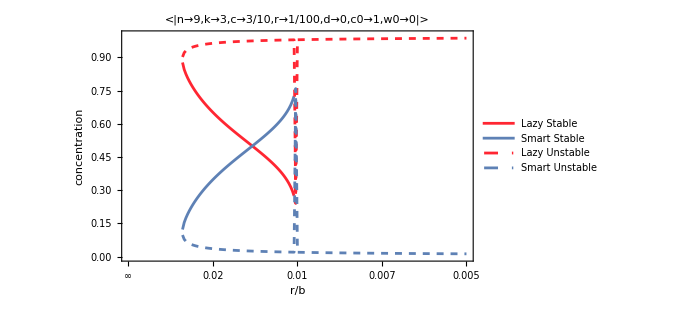

```mathematica
ClearAll[n,k,c,r,b,c0,w0,d,δ];

δ=1/100;
ind=Range[0,2,δ];
sys={"Lazy","Smart"};
par=KeyDrop[$ParameterSets[[2]],{"Name",b}];

data=Table[
Block[{la,tr,fp,jacobi,eval,n=par@n,k=par@k,b},(* NOTE: Substitute the value of n and k into the equations so that If-s and Sum-s can be evaluated in fLa, fTr, fSm. *)
b=i;
fp=N@Solve[{fLa[la,tr]==0,fTr[la,tr]==0,fSm[la,tr]==0,0<la<1,tr==0}/.par,{la,tr}];
If[fp=={},{},
jacobi=D[{fLa[la,tr],fTr[la,tr]},{{la,tr}}]/.fp/.par;
eval=First@MaximalBy[Eigenvalues@#,Re@*N]&/@jacobi;(* NOTE: Get dominant eigenvalues *)
eval=Thread@(Re@eval<0);(* NOTE: True if stable, False if unstable *)
fp=N@Chop@({la,1-la-tr}/.fp);
Thread[eval->fp]]
],{i,ind}];

stable=DeleteCases[{ind,#}ᵀ&/@Transpose[True/.data/.True->{{},{}}],{_,{}},{2}];
unstable=DeleteCases[{ind,#}ᵀ&/@Transpose[False/.data/.False->{{},{}}],{_,{}},{2}];

labels=Flatten[(StringRiffle/@Thread@{sys,#})&/@{"Stable","Unstable"}];
styles=MapThread[Directive,{Lookup[colors,Flatten@Table[sys,2]],{{},{},Dashed,Dashed}}];
strategy=Flatten@Table[sys,2];
ticks=Charting`ScaledFrameTicks[{Identity,Identity}][0,Max@ind];
ticks=Quiet[{#[[1]],If[#[[3,1]]==.01,NumberForm[r/#[[1]]/.par,1],""],#[[3]]}&/@ticks]/.ComplexInfinity->∞;

plot=Framed[plotB=ListLinePlot[Join[stable,unstable],
PlotRange->{{0,Max@ind},{0,1}},PlotRangePadding->{Scaled[.02],Scaled[.03]},
PlotStyle->styles,
PlotHighlighting->None,
PlotLegends->LineLegend[labels],
Frame->True,FrameStyle->Directive[AbsoluteThickness@1,Black],Axes->False,
FrameTicks->{{Automatic,Automatic},{ticks,All}},
FrameLabel->{{"concentration",None},{"r/b","b"}},
PlotLabel->par,ImageSize->500,Background->White,LabelStyle->Directive[12,Black]
],FrameStyle->None,Background->White]
```

#### Combined Trusty & Smart (simplified)

Calculating fixed points separately for the Lazy-Trusty pair and for the Lazy-Smart pair.

Ignoring the boundary unstable fixed point tr==1 or sm==1 when there is 1 or 3 solutions.

```mathematica
ClearAll[n,k,c,r,b,c0,w0,d,δ];

δ=1/1000;
ind=Range[3/10,1,δ];
sys={"Trusty","Smart"};
par=<|n->9,k->3,c->7/10,r->1/6,c0->3,w0->0|>;

(* NOTE: Collect fixed points only for Trusty. *)
dataTr=Transpose@Table[Block[{la,tr,fp,n=par@n,k=par@k},
(* NOTE: Allow Trusty to be 1, by allowing Lazy to be 0. *)
fp=Solve[{fLa[la,tr]==0,fTr[la,tr]==0,0<=la<1,0<tr<=1,la+tr==1}/.par,{la,tr},Reals];
fp=Sort@N@(tr/.fp);
(* NOTE: When there are 1 or 3 solutions, ignore the boundary unstable fixed point. *)
(* NOTE: Sort results in: {unstable, stable} pairs. *)
Sort@Switch[Length@fp,0|1,{Missing[],Missing[]},2,fp,3,DeleteCases[fp,1|1.],_,Print@"ERROR! More than 3 solutions.";fp]
],{b,ind}];

(* NOTE: Collect fixed points only for Smart. *)
dataSm=Transpose@Table[Block[{la,tr,fp,n=par@n,k=par@k},
(* NOTE: Allow Smart to be 1, by allowing Lazy to be 0. *)
fp=Solve[{fLa[la,tr]==0,fTr[la,tr]==0,0<=la<1,tr==0}/.par,{la,tr},Reals];
fp=Sort@N@(1-la/.fp);
(* NOTE: When there are 1 or 3 solutions, ignore the boundary unstable fixed point. *)
(* NOTE: Sort results in: {unstable, stable} pairs. *)
Sort@Switch[Length@fp,0|1,{Missing[],Missing[]},2,fp,3,DeleteCases[fp,1|1.],_,Print@"ERROR! More than 3 solutions.";fp]
],{b,ind}];

dataLa={{#,Missing[]}&/@ind,{#,0}&/@ind};

ticks=Charting`ScaledFrameTicks[{Identity,Identity}][0,Max@ind];
ticks=Quiet[{#[[1]],If[#[[3,1]]==.01,NumberForm[1/#[[1]]/.par,2],""],#[[3]]}&/@ticks]/.ComplexInfinity->∞;
```

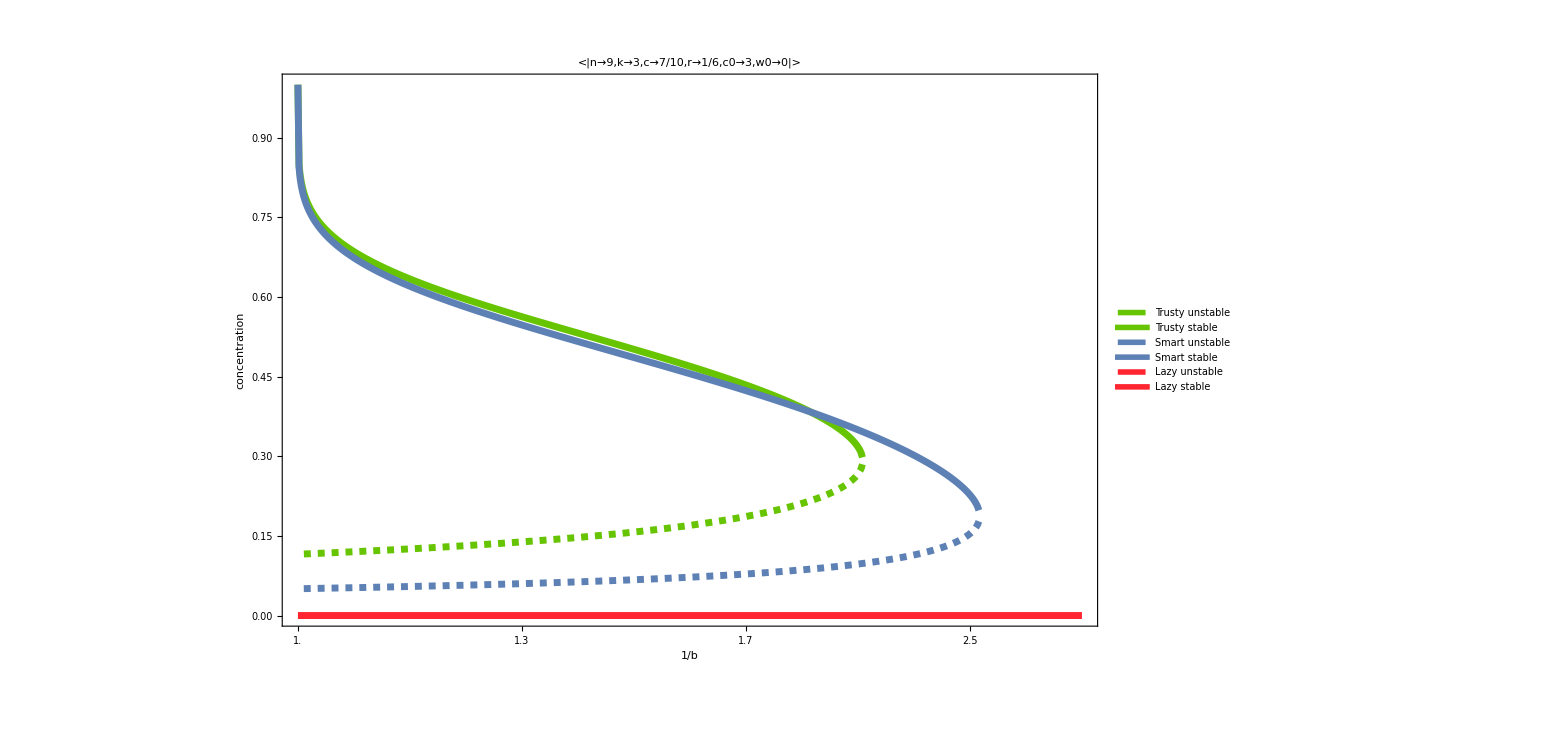

```mathematica
plot=Framed[ListLinePlot[N@Join[dataTr,dataSm,dataLa],
DataRange->MinMax@ind,
PlotRange->{MinMax@ind,{0,1}},PlotRangePadding->{Scaled[.02],Scaled[.03]},
PlotHighlighting->"Dropline",
PlotStyle->{
Directive[colors@"Trusty",lines@"Unstable",AbsoluteThickness@5],Directive[colors@"Trusty",lines@"Stable",AbsoluteThickness@5],
Directive[colors@"Smart",lines@"Unstable",AbsoluteThickness@5],Directive[colors@"Smart",lines@"Stable",AbsoluteThickness@5],
Directive[colors@"Lazy",lines@"Unstable",AbsoluteThickness@5],Directive[colors@"Lazy",lines@"Stable",AbsoluteThickness@5]
},
PlotLegends->{"Trusty unstable","Trusty stable","Smart unstable","Smart stable","Lazy unstable","Lazy stable"},
Frame->True,FrameStyle->Directive[AbsoluteThickness@2,Black],Axes->False,
FrameTicks->{{Automatic,Automatic},{ticks,Automatic}},
FrameLabel->{{"concentration",None},{"1/b",None}},
ScalingFunctions->{"Reverse",Identity},
PlotLabel->par,ImageSize->1200,Background->White,LabelStyle->Directive[26,Black],
ImagePadding->{{100,10},{100,10}}
],FrameStyle->None,Background->White];
Magnify[plot,.4]
```

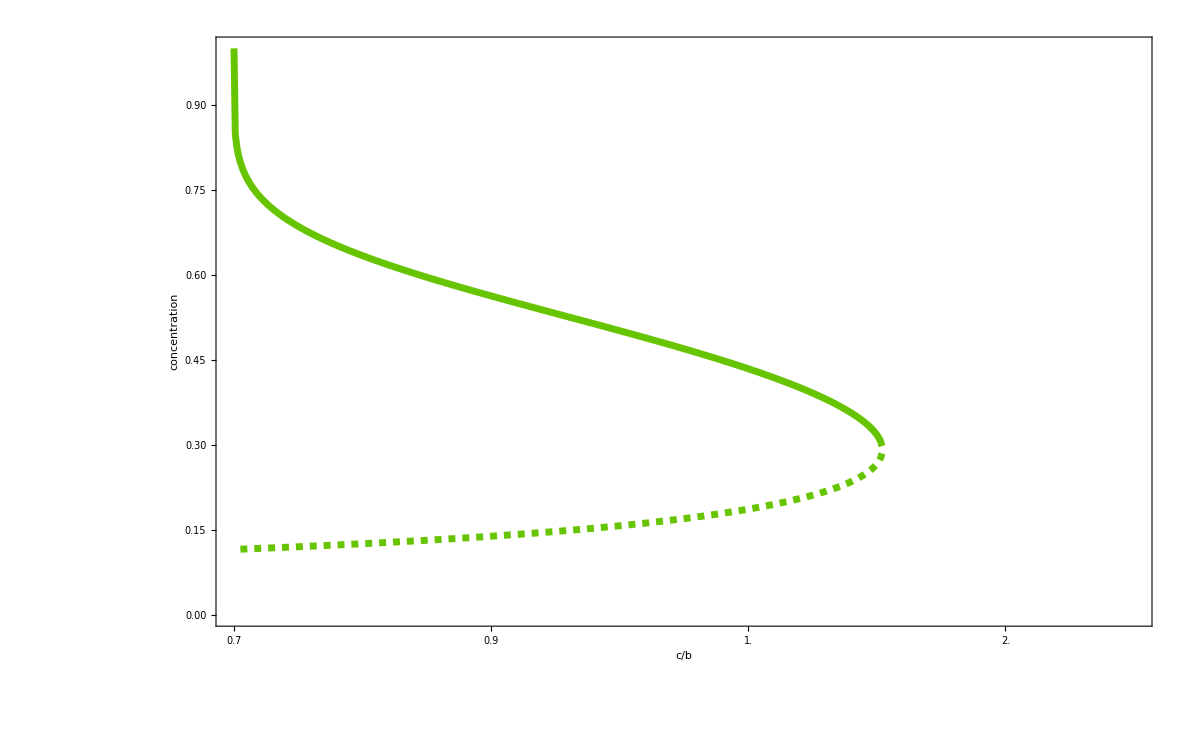
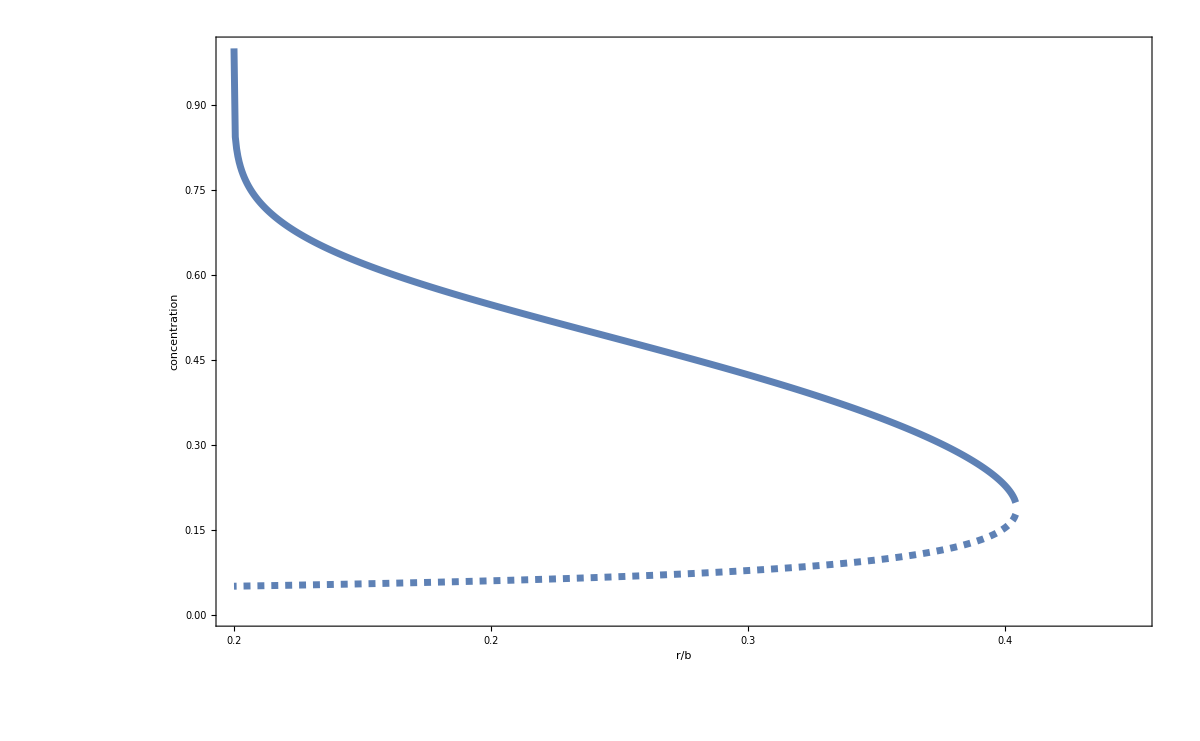

```mathematica
Block[{var,data,strat=#,ticks,plot},
{var,data}=Switch[strat,"Trusty",{c,dataTr},"Smart",{r,dataSm}];
ticks=Charting`ScaledFrameTicks[{Identity,Identity}][0,Max@ind];
ticks=Quiet[{#[[1]],If[#[[3,1]]==.01,NumberForm[var/#[[1]]/.par,1],""],#[[3]]}&/@ticks]/.ComplexInfinity->∞;
plot=ListLinePlot[data,
DataRange->MinMax@ind,
PlotRange->{MinMax@ind,{0,1}},PlotRangePadding->{Scaled[.02],Scaled[.03]},
PlotHighlighting->None,
PlotStyle->{Directive[colors@strat,lines@"Unstable",AbsoluteThickness@5],Directive[colors@strat,lines@"Stable",AbsoluteThickness@5]},
Frame->True,FrameStyle->Directive[AbsoluteThickness@2,Black],Axes->False,
FrameTicks->{{Automatic,Automatic},{ticks,All}},
FrameLabel->{{"concentration",None},{Row@{var,"/",b},b}},
ScalingFunctions->{"Reverse",Identity},
(*PlotLabel->par,*)ImageSize->1200,Background->White,LabelStyle->Directive[26,"Helvetica",Black]
];
Magnify[plot,.4]
]&/@{"Trusty","Smart"}
```